Si può automatizzare la ricerca della biforcazione. Per determinare la biforcazione n-esima, si parte da un appropriato valore di μ inferiore a quello di biforcazione (stimato ad occhio) e si confrontano, per un N opportunamente grande, le iterate N-esima e (N+2^n)-esima di uno stesso punto inziale. Se sono molto vicini, non siamo ancora alla biforcazione, e bisogna aumentare μ. Appena cominciano ad allontanarsi, siamo arrivati alla biforcazione.

```mathematica
ClearAll["Global`*"]
```

```mathematica
f[μ_,x_]:= μ x(1-x)
fn[μ_,x_,n_]:=Nest[f[μ,#]&,x,n]
dist[μ_,x0_,Ν_,n_]:=Abs[fn[μ,x0,Ν]-fn[μ,x0,Ν+2^n]]
indagine[n_,{min_,max_,step_}]:=ParallelTable[{μ,dist[μ,0.4,10^6,n]},{μ,min,max,step}]
```

URLFetch::invhttp: A library error occurred. The raw details are: "libcurl error (6): Could not resolve host: www.wolframcloud.com"

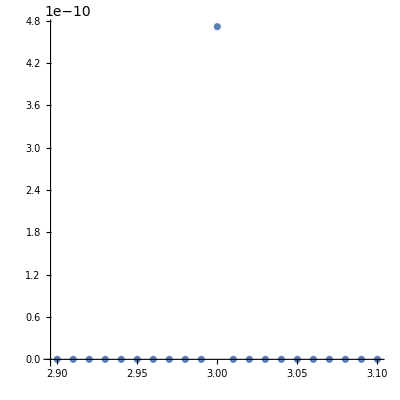

```mathematica
ListPlot[indagine[2,{2.9,3.1,10^-2}],AspectRatio->1]
```

```mathematica
Module[
{
ind=indagine[2,{2.99,3.01,10^-3}],
val,
spike
},
val=Last/@ind;
spike=Max@val;
Cases[ind,{_,spike}]
]
```

{{3.,4.71716×10^-10}}

Per quanto riguarda la richiesta, userei questo

```mathematica
SequencePosition[Table[{RandomReal[],0},2000],Table[{_,0},150],Overlaps->False]
```

{{1,150},{151,300},{301,450},{451,600},{601,750},{751,900},{901,1050},{1051,1200},{1201,1350},{1351,1500},{1501,1650},{1651,1800},{1801,1950}}